```mathematica
(** λ1 = Lower bound of wavelength for transition
	λ2 = Upper bound of wavelength for transition **)
λ1 = 794.9686*^-9
λ2 = 794.9897*^-9
c = 2.99792*^8
(** Convert wavelength to frequency **)
ν1 = c/λ1 
ν2 = c/λ2
(** Find the difference in the frequencies **)
νdiff = ν1 - ν2
λdiff = λ2 -λ1
```

7.94969×10^-7

7.9499×10^-7

2.99792×10^8

3.77112×10^14

3.77102×10^14

1.0009×10^10

2.11×10^-11

```mathematica
NumberForm[λdiff,16]
```

1.873000000000033×10^-10

```mathematica
NumberForm[λdiff,16]
```

1.873000000000033×10^-10

```mathematica
(** Find the distance between tick marks **)
tickDistance = λdiff/4
```

5.275×10^-12

## The Rb-87 D1 Line (794.979 nm)

```mathematica
(** Convert the D1 line to a Frequency **)
λD187= 794.979*^-9
c = 2.99792*^8
νD187 = c /λD187
```

7.94979×10^-7

2.99792×10^8

3.77107×10^14

```mathematica
(** Add the two hyperfine transition frequencies to the D1 line frequency**)
νUpToF2=305.44*^6
νDownToF1=4.2717*^6
νGF1ToEF2 = νD187+νUpToF2 + νDownToF1
```

3.0544×10^8

4.2717×10^6

3.77107×10^14

```mathematica
(** Convert this frequency back to a wavelength **)
λGF1ToEF2=c/νGF1ToEF2
```

7.94978×10^-7

```mathematica
(** This seems like it is too long of a wavelength. The g1->e2 transition is very close to 7.949686*10^-7
Our number calculated above, (7.94978*10-7) should be LESS THAN the value of the next tick mark on the graph. Let's calculate that.**)
nextTick=λ1 +tickDistance
```

7.94974×10^-7

```mathematica
(** Since the next tick is smaller than our calculated Wavelength, that indicates that this method is not the way to go about it. **)
```

## Finding all of the frequencies of the different transitions.

```mathematica
λD1= 794.979*^-9
c = 2.99792*^8
νD1 = c /λD1
```

7.94979×10^-7

2.99792×10^8

3.77107×10^14

```mathematica
rb85Detunings={1.7708*^9,1.2649*^9,210.92*^6,150.66*^6};
rb87Detunings={4.2717*^9,2.5630*^9,509.06*^6,305.44*^6};

rb85frequencyShifts={
νD1+rb85Detunings[[1]]-rb85Detunings[[3]],
νD1+rb85Detunings[[1]]+rb85Detunings[[4]],
νD1-rb85Detunings[[2]]-rb85Detunings[[3]],
νD1-rb85Detunings[[2]]+rb85Detunings[[4]]
}
rb85wavelengths=rb85frequencyShifts

rb87frequencyShifts={
νD1+rb87Detunings[[1]]-rb87Detunings[[3]],
νD1+rb87Detunings[[1]]+rb87Detunings[[4]],
νD1-rb87Detunings[[2]]-rb87Detunings[[3]],
νD1-rb87Detunings[[2]]+rb87Detunings[[4]]
}
rb87wavelengths=rb87frequencyShifts
```

{3.77108×10^14,3.77109×10^14,3.77105×10^14,3.77106×10^14}

{3.77108×10^14,3.77109×10^14,3.77105×10^14,3.77106×10^14}

{3.77111×10^14,3.77111×10^14,3.77104×10^14,3.77105×10^14}

{3.77111×10^14,3.77111×10^14,3.77104×10^14,3.77105×10^14}

```mathematica
For[i=1, i <= Length[rb85frequencyShifts],i++,
rb85wavelengths[[i]]=c/rb85frequencyShifts[[i]]
]
For[i=1, i <= Length[rb87frequencyShifts],i++,
rb87wavelengths[[i]]=c/rb87frequencyShifts[[i]]
]
```

```mathematica
rb87wavelengths
```

{7.94971×10^-7,7.94969×10^-7,7.94985×10^-7,7.94984×10^-7}

```mathematica
rbWavelengths = Sort[Join[rb85wavelengths,rb87wavelengths]]
```

{7.94969×10^-7,7.94971×10^-7,7.94975×10^-7,7.94976×10^-7,7.94981×10^-7,7.94982×10^-7,7.94984×10^-7,7.94985×10^-7}

```mathematica
SetPrecision[rbWavelengths,8]
```

{7.9496935×10^-7,7.9497107×10^-7,7.9497495×10^-7,7.9497571×10^-7,7.9498135×10^-7,7.9498211×10^-7,7.9498376×10^-7,7.9498548×10^-7}

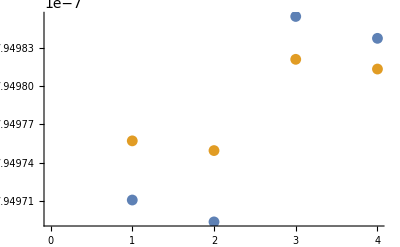

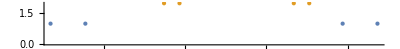

```mathematica
ListPlot[{rb87wavelengths,rb85wavelengths}]
NumberLinePlot[{rb87wavelengths,rb85wavelengths}]
```